```mathematica
model = a*x^b  ;
```

```mathematica
data = Import["E:\\Alessio\\Desktop\\Computazionale\\es5\\data_trapezio.txt","Table"];
Trapezio = Take[data][[All,{1,3}]];
DELTATrapezio = Take[data,-500][[All,{2,4}]];
```

```mathematica
linetrap=FindFit[DELTATrapezio, model,{a,b},x]
```

{a→306.158,b→2.01299}

```mathematica
data = Import["E:\\Alessio\\Desktop\\Computazionale\\es5\\data_simpson.txt","Table"];
Simpson= Take[data][[All,{1,3}]];
DELTASimpson= Take[data,-250][[All,{2,4}]];
```

```mathematica
linesimp=FindFit[DELTASimpson, model,{a,b},x]
```

{a→18190.5677123177875897954973905986330744754,b→4.050005112734025023622249823558704820434561}

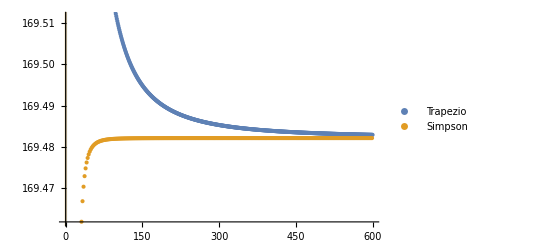

```mathematica
Show[{ListPlot[{Trapezio,Simpson}, PlotLegends->{"Trapezio", "Simpson"},PlotRange->Automatic],Plot[{model/.linetrap,model/.linesimp},{x,0,1},PlotStyle->Opacity[0.4]]}]
```

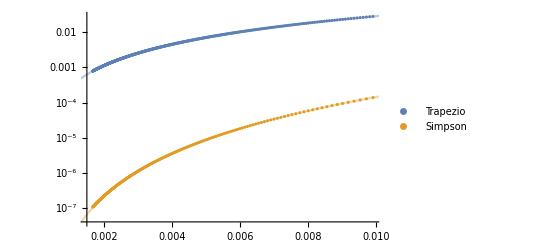

```mathematica
Show[{ListLogPlot[{DELTATrapezio,DELTASimpson}, PlotLegends->{"Trapezio", "Simpson"},PlotRange->All],LogPlot[{model/.linetrap,model/.linesimp},{x,0,0.02},PlotStyle->Opacity[0.4]]}]
```

```mathematica
data= Import["E:\\Alessio\\Desktop\\Computazionale\\es5\\data_legendre.txt","Table"];
DELTALegendre = Take[data][[All,{1,3}]];
```

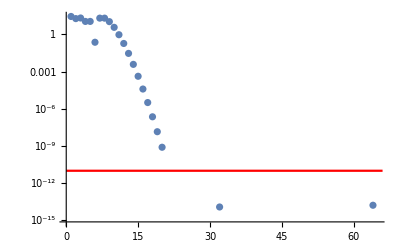

```mathematica
Show[{ListLogPlot[{DELTALegendre}, PlotRange->{{0,65},Automatic}],LogPlot[10^(-11),{x,0,66},PlotStyle->Red]}]
```

```mathematica
data =Import["E:\\Alessio\\Desktop\\Computazionale\\es5\\data_romberg.txt","Table"];
Romberg1 = Take[data,{8,20}][[All,{1,2}]];
Romberg2 = Take[data,{7,13}][[All,{1,3}]];
Romberg3 = Take[data,{5,12}][[All,{1,4}]];
```

```mathematica
lineromb1=FindFit[Romberg1, model,{a,b},x]
lineromb2=FindFit[Romberg2, model,{a,b},x]
lineromb3=FindFit[Romberg3, model,{a,b},x,MaxIterations->1000]
```

{a→303.49613551345764654621943697720585485415,b→2.0112856965860843825371036480181911239709}

{a→21636.4255211550286705683718244405198712,b→4.08589503858776114175317349989138107664}

{a→3.2875929581250265794685566662318206×10^7,b→6.15936426673258173860599871679784347}

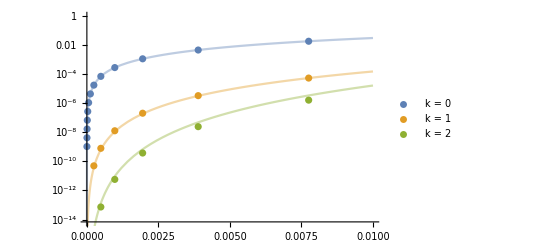

```mathematica
Show[{ListLogPlot[{Romberg1,Romberg2,Romberg3},PlotLegends->{"k = 0","k = 1","k = 2"},PlotRange->{{0,0.01},All}],LogPlot[{model/.lineromb1,model/.lineromb2,model/.lineromb3},{x,0,0.01},PlotStyle->Opacity[0.4]]}]
```

```mathematica
g[x_]= x^2 + x*Sin[4*x]
```

x^2+x Sin[4 x]

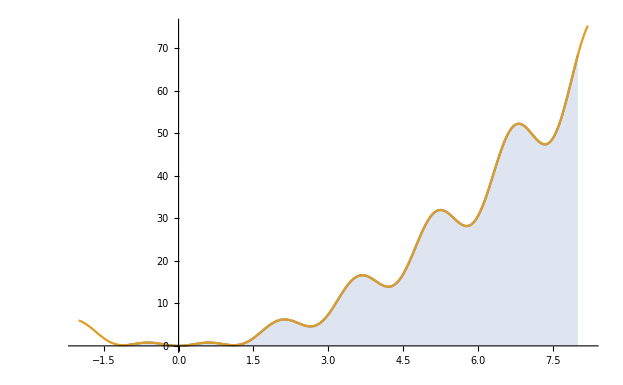

```mathematica
Plot[{If[-1<x<8, g[x]],g[x]},{x,-2,8.2}, Filling->{1->Axis}]
```

```mathematica
Integrate[g[x],{x,-1,8}]
```

1/16 (2736-4 Cos[4]-32 Cos[32]+Sin[4]+Sin[32])

```mathematica
N[%]
```

169.482

```mathematica
f[y_]:=NIntegrate[g[x],{x,2,y}]
```

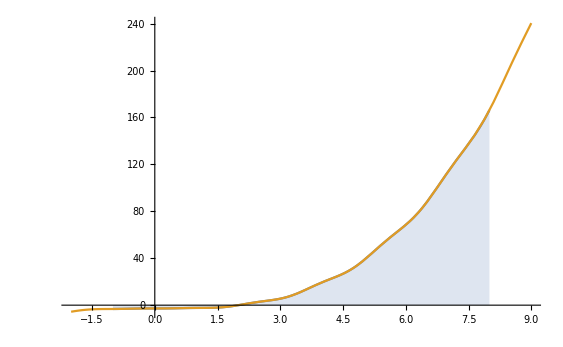

```mathematica
Plot[{If[-1<x<8, f[x]],f[x]},{x,-2,9}, Filling->{1->Axis}]
```